```mathematica
ClearAll["Global`*"]
```

```mathematica
Pfaffian[Mat_]:=Module[{A, N, ip, pfaff},
A=Mat;
N=Dimensions[A][[1]];
If[OddQ[N], Return[0]];
pfaff=1;
For[i=1, i<N-1, i+=2,
(*find out the maximum entry in the column i, starting from row i+1*)
ip=i+Position[Abs[A[[i+1;;, i]]], Max[Abs[A[[i+1;;,i]]]]][[1,1]];
(*if the maximum entry is not at i+1, permute the matrix so that it is*)
If[i+1 ≠ ip, 
(*Interchange rows and columns in A*)
A[[{i+1, ip},;;]]=A[[{ip,i+1},;;]]; 
A[[;;,{i+1, ip}]]=A[[;;,{ip,i+1}]];
(*interchange contributes det(P)=-1*)
pfaff=-pfaff;
];
(*Multiply with every other entry on the diagonal*)
pfaff = pfaff*A[[i,i+1]];
(*Build the Gauss vector*)
A[[i+2;;,i]]=A[[i+2;;,i]]/A[[i+1,i]];
(*Update the remainder of the matrix using an outer product skew-symmetric update. Note that
column and row i+1 are not affected by the update*)
A[[i+2;; , i+2;; ]]+=(#-Transpose[#])&@Outer[Times,A[[i+2;;,i]],A[[i+2;;,i+1]]]
(* The above is much faster than this construct for me: 
Transpose[{A[[i+2;;,i]]}].{A[[i+2;;,i+1]]}-Transpose[{A[[i+2;;,i+1]]}].{ A[[i+2;;,i]]};*)
];
Return[pfaff*A[[N-1,N]]]
]
```

## 有効4バンド模型の計算

### ϵ(q0)=0の場合

#### 4x4ハミルトニアンと解析解

```mathematica
hT1[q0_,σ_]:=Simplify[{{0,-s*ⅇ^(-ⅈ ϕ/4),s*ⅇ^(ⅈ ϕ/4),0},
{-s ⅇ^(ⅈ ϕ/4),0,0,(-1)^q0 s ⅈ ⅇ^(-ⅈ ϕ/4)},
{s ⅇ^(-ⅈ ϕ/4),0,0,(-1)^q0 s ⅈ ⅇ^(ⅈ ϕ/4)},
{0,(-1)^q0 s*(-ⅈ)ⅇ^(ⅈ ϕ/4),(-1)^q0 s*(-ⅈ) ⅇ^(-ⅈ ϕ/4),0}}/.{s->ⅇ^(ⅈ π(1-σ)/4)},{q0∈Integers,σ∈Reals,ϕ∈Reals,σ^2==1}];
```

```mathematica
hT1p[q0_,σ_]:=Module[{s},
s=If[σ>0,1,ⅈ];
s{{-ⅇ^(ⅈ ϕL/2),ⅈ(-1)^q0 ⅇ^(ⅈ ϕR/2)},{ⅇ^(-ⅈ ϕL/2),ⅈ(-1)^q0 ⅇ^(-ⅈ ϕR/2)}}
]
hT1[q0_,σ_]:=Simplify[
Join[Join[ConstantArray[0,{2,2}],hT1p[q0,σ]†,2],
Join[hT1p[q0,σ],ConstantArray[0,{2,2}],2]],
{q0∈Integers,ϕR∈Reals,ϕL∈Reals}
]
```

```mathematica
Simplify[-Abs[Cos[(ϕ+π)/4]]-Abs[Cos[(ϕ-π)/4]],{π≤ϕ≤2π}]
```

-√2 Sin[ϕ/4]

```mathematica
hT1=Module[{hT1p},Simplify[
hT1p=s{{-ⅇ^(ⅈ ϕL/2),ⅈ(-1)^q0 ⅇ^(ⅈ ϕR/2)},{ⅇ^(-ⅈ ϕL/2),ⅈ(-1)^q0 ⅇ^(-ⅈ ϕR/2)}};
Join[Join[ConstantArray[0,{2,2}],hT1p†,2],
Join[hT1p,ConstantArray[0,{2,2}],2]],
{q0∈Integers,ϕR∈Reals,ϕL∈Reals}
]];
pm[σ_]:=If[σ≥0,"+","-"];
```

```mathematica
Module[{test,kernel},
Do[
Print["s=",s,", q0=",q0];
Do[
test=Simplify[(DiagonalMatrix[2{ϵ,ϵ,ϵ,ϵ}]-hT1)/.{ϵ->σ1/(√2)Cos[(ϕR-ϕL)/4]+σ2/(√2)Sin[(ϕR-ϕL)/4]}];
kernel=FullSimplify[NullSpace[test]][[1]];
kernel=kernel/kernel[[1]];
Print[pm[σ1],pm[σ2],", ",kernel,", ",Simplify[kernel=={1,σ1 σ2(-1)^q0,-σ1 s ⅇ^(-σ1 σ2(ⅈ π)/4) ⅇ^(ⅈ/4(ϕL+ϕR)), σ1 s ⅇ^(σ1 σ2(ⅈ π)/4) ⅇ^(-ⅈ/4(ϕL+ϕR))}]],
{σ1,{1,-1}},{σ2,{1,-1}}
],
{s,{1,ⅈ}},{q0,{0,1}}
]
]
```

s=1, q0=0

++, {1,1,(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

+-, {1,-1,-(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

-+, {1,-1,(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

--, {1,1,-(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

s=1, q0=1

++, {1,-1,(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

+-, {1,1,-(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

-+, {1,1,(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

--, {1,-1,-(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

s=ⅈ, q0=0

++, {1,1,-(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

+-, {1,-1,-(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

-+, {1,-1,(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

--, {1,1,(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

s=ⅈ, q0=1

++, {1,-1,-(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

+-, {1,1,-(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

-+, {1,1,(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

--, {1,-1,(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

```mathematica
Module[{test,kernel},
Do[
Print["s=",s,", q0=",q0];
Do[
test=Simplify[(DiagonalMatrix[2{ϵ,ϵ,ϵ,ϵ}]-hT1)/.{ϵ->σ1 Cos[(ϕR-ϕL+σ2 π)/4]}];
kernel=FullSimplify[NullSpace[test]][[1]];
kernel=kernel/kernel[[1]];
Print[pm[σ1],pm[σ2],", ",kernel,", ",Simplify[kernel=={1,σ2(-1)^(q0-1),-σ1 s ⅇ^(σ2(ⅈ π)/4) ⅇ^(ⅈ/4(ϕL+ϕR)), σ1 s ⅇ^(-σ2(ⅈ π)/4) ⅇ^(-ⅈ/4(ϕL+ϕR))}]],
{σ1,{1,-1}},{σ2,{1,-1}}
],
{s,{1,ⅈ}},{q0,{0,1}}
]
]
```

s=1, q0=0

++, {1,-1,-(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

+-, {1,1,(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

-+, {1,-1,(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

--, {1,1,-(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

s=1, q0=1

++, {1,1,-(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

+-, {1,-1,(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

-+, {1,1,(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

--, {1,-1,-(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

s=ⅈ, q0=0

++, {1,-1,-(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

+-, {1,1,-(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

-+, {1,-1,(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

--, {1,1,(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

s=ⅈ, q0=1

++, {1,1,-(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

+-, {1,-1,-(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

-+, {1,1,(-1)^(3/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(1/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

--, {1,-1,(-1)^(1/4) ⅇ^(1/4 ⅈ (ϕL+ϕR)),-(-1)^(3/4) ⅇ^(-1/4 ⅈ (ϕL+ϕR))}, True

#### 解析解の基底を用いたInversion parityの計算(ϕ=-2π, 0)

```mathematica
(*umat[q0_,σ_]:=MapThread[Simplify[1/2{#2 ⅈ(-1)^(q0-1)ⅇ^(ⅈ ϕ/2),#1(-1)^q0 s(2Cos[(ϕ+#2 π)/4])/(1-#2 ⅈ ⅇ^(-ⅈ ϕ/2)),-#1 #2(-1)^q0 s ⅈ(2Cos[(ϕ+#2 π)/4])/(1-#2 ⅈ ⅇ^(-ⅈ ϕ/2)),1}/.{s->ⅇ^(ⅈ π(1-σ)/4)},{q0∈Integers,σ∈Reals,ϕ∈Reals,σ^2==1}]&,{{1,1,-1,-1},{1,-1,1,-1}}]//Transpose;
Simplify[ConjugateTranspose[umat[q0,σ]].umat[q0,σ]/.{q0->1},{q0∈Integers,σ∈Reals,ϕ∈Reals,σ^2==1}]
eigvals=Diagonal[Simplify[(ConjugateTranspose[umat[q0,σ]].hT1[q0,σ].umat[q0,σ])/.{q0->1,σ->1},{q0∈Integers,ϕ∈Reals}]]
Plot[eigvals,{ϕ,-2π,2π}]*)
iop={{0,1,0,0},{1,0,0,0},{0,0,(-1)^(q0-1),0},{0,0,0,(-1)^q0}};
Do[
Print[{q0,σ}];
Do[
Print["ϕ=",ϕ,", UIU=",Simplify[(ConjugateTranspose[umat[q0,σ]].iop.umat[q0,σ])]],
{ϕ,{-2π,0}}
],
{q0,{0,1}},{σ,{1,-1}}
]
```

{0,1}

ϕ=-2 π, UIU=ConjugateTranspose[umat[0,1]].{{0,1,0,0},{1,0,0,0},{0,0,-1,0},{0,0,0,1}}.umat[0,1]

ϕ=0, UIU=ConjugateTranspose[umat[0,1]].{{0,1,0,0},{1,0,0,0},{0,0,-1,0},{0,0,0,1}}.umat[0,1]

{0,-1}

ϕ=-2 π, UIU=ConjugateTranspose[umat[0,-1]].{{0,1,0,0},{1,0,0,0},{0,0,-1,0},{0,0,0,1}}.umat[0,-1]

ϕ=0, UIU=ConjugateTranspose[umat[0,-1]].{{0,1,0,0},{1,0,0,0},{0,0,-1,0},{0,0,0,1}}.umat[0,-1]

{1,1}

ϕ=-2 π, UIU=ConjugateTranspose[umat[1,1]].{{0,1,0,0},{1,0,0,0},{0,0,1,0},{0,0,0,-1}}.umat[1,1]

ϕ=0, UIU=ConjugateTranspose[umat[1,1]].{{0,1,0,0},{1,0,0,0},{0,0,1,0},{0,0,0,-1}}.umat[1,1]

{1,-1}

ϕ=-2 π, UIU=ConjugateTranspose[umat[1,-1]].{{0,1,0,0},{1,0,0,0},{0,0,1,0},{0,0,0,-1}}.umat[1,-1]

ϕ=0, UIU=ConjugateTranspose[umat[1,-1]].{{0,1,0,0},{1,0,0,0},{0,0,1,0},{0,0,0,-1}}.umat[1,-1]

```mathematica
Simplify[(Conjugate[umat[q0,σ][[All,1]]-ⅈ umat[q0,σ][[All,4]]].iop.(umat[q0,σ][[All,1]]-ⅈ umat[q0,σ][[All,4]]))/.{ϕ->2π},{q0∈Integers,σ∈Reals,σ^2==1}]
Simplify[(Conjugate[umat[q0,σ][[All,1]]+ⅈ umat[q0,σ][[All,2]]].iop.(umat[q0,σ][[All,1]]+ⅈ umat[q0,σ][[All,2]]))/.{ϕ->0},{q0∈Integers,σ∈Reals,σ^2==1}]
```

-2 (-1)^q0

-2 (-1)^q0

### ϵ(q0)≠0の場合

#### エネルギーバンドの数値解

ϵ=-0.5

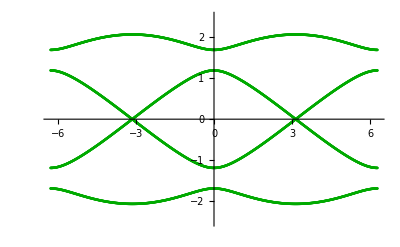

ϵ=0.

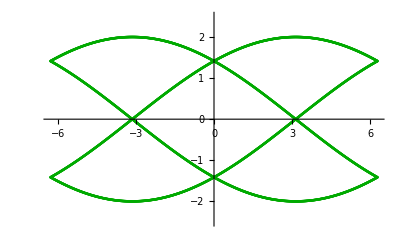

ϵ=0.5

-Graphics-

```mathematica
en=DiagonalMatrix[{0,0,ϵ,-ϵ}];
Do[
Print["ϵ=",ϵ];
eigvals=Table[{ϕ,Sort[Eigenvalues[(hT1[1,1]/.{ϕL->-ϕ/2,ϕR->ϕ/2})+en]][[i]]},{i,1,4},{ϕ,-2π,2π,π/256}];
Print@ListPlot[eigvals,PlotRange->{-2.5,2.5},PlotStyle->Darker[Green]],
{ϵ,{-0.5,0.0,0.5}}
]
```

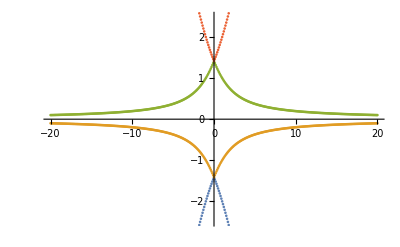

```mathematica
eigvals=Table[{ϵ,Sort[Eigenvalues[(hT1[1,-1]+en)/.{ϕL->0,ϕR->0}]][[i]]},{i,1,4},{ϵ,-20,20,0.1}];
Print@ListPlot[eigvals,PlotRange->{-2.5,2.5}]
```

#### GS fermion parityの計算

```mathematica
hamil=(hT1[q0,σ]/.{ϕL->-ϕ/2,ϕR->ϕ/2})+en;
phop={{ⅇ^(ⅈ ϕ/2)σ,0,0,0},{0,-ⅇ^(-ⅈ ϕ/2)σ,0,0},{0,0,0,1},{0,0,1,0}};
Do[
Print[{q0,σ}];
Print["HC+CH=",MatrixForm[Simplify[hamil.phop+phop.hamil*,{ϕ∈Reals,ϵ∈Reals}]]];
(*Print@Plot[Pfaffian[hamil.phop],{ϕ,-2π,2π},PlotLabel->Pfaffian];*),
{q0,{0,1}},{σ,{1,-1}}
]
Print[MatrixForm[hamil.phop]];
Print["FP=",Simplify[Pfaffian[hamil.phop],{q0∈Integers,ϕ∈Reals}]];
```

{0,1}

HC+CH=(0 | 0 | ⅇ^(-(ⅈ ϕ)/4)-ⅇ^((ⅈ ϕ)/4) | ⅇ^((ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2))
0 | 0 | -ⅈ ⅇ^(-(ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2)) | -ⅈ ⅇ^(-(3 ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2))
ⅇ^(-(ⅈ ϕ)/4)-ⅇ^((ⅈ ϕ)/4) | -ⅈ ⅇ^(-(ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2)) | 0 | 0
ⅇ^((ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2)) | -ⅈ ⅇ^(-(3 ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2)) | 0 | 0)

{0,-1}

HC+CH=(0 | 0 | ⅈ ⅇ^(-(ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2)) | -ⅈ ⅇ^((ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2))
0 | 0 | -ⅇ^(-(ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2)) | -ⅇ^(-(3 ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2))
ⅈ ⅇ^(-(ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2)) | -ⅇ^(-(ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2)) | 0 | 0
-ⅈ ⅇ^((ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2)) | -ⅇ^(-(3 ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2)) | 0 | 0)

{1,1}

HC+CH=(0 | 0 | ⅇ^(-(ⅈ ϕ)/4)-ⅇ^((ⅈ ϕ)/4) | ⅇ^((ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2))
0 | 0 | ⅈ ⅇ^(-(ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2)) | ⅈ ⅇ^(-(3 ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2))
ⅇ^(-(ⅈ ϕ)/4)-ⅇ^((ⅈ ϕ)/4) | ⅈ ⅇ^(-(ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2)) | 0 | 0
ⅇ^((ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2)) | ⅈ ⅇ^(-(3 ⅈ ϕ)/4) (1+ⅇ^((ⅈ ϕ)/2)) | 0 | 0)

{1,-1}

HC+CH=(0 | 0 | ⅈ ⅇ^(-(ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2)) | -ⅈ ⅇ^((ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2))
0 | 0 | ⅇ^(-(ⅈ ϕ)/4)+ⅇ^((ⅈ ϕ)/4) | ⅇ^(-(ⅈ ϕ)/4)+ⅇ^(-(3 ⅈ ϕ)/4)
ⅈ ⅇ^(-(ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2)) | ⅇ^(-(ⅈ ϕ)/4)+ⅇ^((ⅈ ϕ)/4) | 0 | 0
-ⅈ ⅇ^((ⅈ ϕ)/4) (-1+ⅇ^((ⅈ ϕ)/2)) | ⅇ^(-(ⅈ ϕ)/4)+ⅇ^(-(3 ⅈ ϕ)/4) | 0 | 0)

(0 | 0 | ⅇ^(-(ⅈ ϕ)/4) Conjugate[If[σ>0,1,ⅈ]] | -ⅇ^((ⅈ ϕ)/4) Conjugate[If[σ>0,1,ⅈ]]
0 | 0 | -ⅈ (-1)^q0 ⅇ^((ⅈ ϕ)/4) Conjugate[If[σ>0,1,ⅈ]] | -ⅈ (-1)^q0 ⅇ^(-(ⅈ ϕ)/4) Conjugate[If[σ>0,1,ⅈ]]
-ⅇ^((ⅈ ϕ)/4) σ If[σ>0,1,ⅈ] | -ⅈ (-1)^q0 ⅇ^(-(ⅈ ϕ)/4) σ If[σ>0,1,ⅈ] | 0 | ϵ
ⅇ^((3 ⅈ ϕ)/4) σ If[σ>0,1,ⅈ] | -ⅈ (-1)^q0 ⅇ^(-(3 ⅈ ϕ)/4) σ If[σ>0,1,ⅈ] | -ϵ | 0)

FP=Pfaffian[{{0,0,ⅇ^(-(ⅈ ϕ)/4) Conjugate[If[σ>0,1,ⅈ]],-ⅇ^((ⅈ ϕ)/4) Conjugate[If[σ>0,1,ⅈ]]},{0,0,-ⅈ (-1)^q0 ⅇ^((ⅈ ϕ)/4) Conjugate[If[σ>0,1,ⅈ]],-ⅈ (-1)^q0 ⅇ^(-(ⅈ ϕ)/4) Conjugate[If[σ>0,1,ⅈ]]},{-ⅇ^((ⅈ ϕ)/4) σ If[σ>0,1,ⅈ],-ⅈ (-1)^q0 ⅇ^(-(ⅈ ϕ)/4) σ If[σ>0,1,ⅈ],0,ϵ},{ⅇ^((3 ⅈ ϕ)/4) σ If[σ>0,1,ⅈ],-ⅈ (-1)^q0 ⅇ^(-(3 ⅈ ϕ)/4) σ If[σ>0,1,ⅈ],-ϵ,0}}]

#### Inversion parityの計算(ϕ=-2π, 0)

```mathematica
Do[
Print["ϕ=",ϕ,", HI-IH=",MatrixForm[Simplify[hamil.iop-iop.hamil,{q0∈Integers,σ∈Integers,σ^2==1}]]],
{ϕ,{-2π,0}}
]
Do[
Print[{q0,σ}];
Do[
{eigvals,eigvecs}=Eigensystem[hamil/.{ϵ->0.2}];
Print["ϕ=",ϕ,", eigvals=",eigvals,", UIU=",Round[Diagonal[Simplify[Inverse[Transpose[eigvecs]].iop.Transpose[eigvecs]]]]],
{ϕ,{-2π,0}}
],
{q0,{0,1}},{σ,{1,-1}}
]
```

ϕ=-2 π, HI-IH=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

ϕ=0, HI-IH=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

{0,1}

ϕ=-2 π, eigvals={1.51774,-1.51774,1.31774,-1.31774}, UIU={-1,1,1,-1}

ϕ=0, eigvals={1.51774,-1.51774,1.31774,-1.31774}, UIU={-1,1,1,-1}

{0,-1}

ϕ=-2 π, eigvals={1.51774,-1.51774,1.31774,-1.31774}, UIU={-1,1,1,-1}

ϕ=0, eigvals={1.51774,-1.51774,1.31774,-1.31774}, UIU={-1,1,1,-1}

{1,1}

ϕ=-2 π, eigvals={1.51774,-1.51774,1.31774,-1.31774}, UIU={1,-1,-1,1}

ϕ=0, eigvals={1.51774,-1.51774,1.31774,-1.31774}, UIU={1,-1,-1,1}

{1,-1}

ϕ=-2 π, eigvals={1.51774,-1.51774,1.31774,-1.31774}, UIU={1,-1,-1,1}

ϕ=0, eigvals={1.51774,-1.51774,1.31774,-1.31774}, UIU={1,-1,-1,1}

#### ϵ(q0)=0, ϕ=2nπでのみ存在する対称性(inversionと反可換)

```mathematica
vop={{-ⅇ^(ⅈ ϕ/2),0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,ⅇ^(-ⅈ ϕ/2)}};
Do[
Print["ϕ=",ϕ,", HV-VH=",MatrixForm[Simplify[hamil.vop-vop.hamil,{q0∈Integers,σ∈Integers,σ^2==1}]]],
{ϕ,{-2π,0}}
]
Do[
Print[{q0,σ}];
Do[
{eigvals,eigvecs}=Eigensystem[N[hamil/.{ϵ->0}]];
Print["ϕ=",ϕ,", eigvals=",eigvals,", UVU=",Diagonal[Round[Inverse[Transpose[eigvecs]].vop.Transpose[eigvecs]]]],
{ϕ,{-2π,0}}
],
{q0,{0,1}},{σ,{1,-1}}
]
```

ϕ=-2 π, HV-VH=(0 | 0 | 0 | 0
0 | 0 | 2 ϵ | 0
0 | -2 ϵ | 0 | 0
0 | 0 | 0 | 0)

ϕ=0, HV-VH=(0 | 0 | 0 | 0
0 | 0 | 2 ϵ | 0
0 | -2 ϵ | 0 | 0
0 | 0 | 0 | 0)

{0,1}

ϕ=-2 π, eigvals={1.41421,1.41421,-1.41421,-1.41421}, UVU={-1,1,-1,1}

ϕ=0, eigvals={1.41421,1.41421,-1.41421,-1.41421}, UVU={1,-1,1,-1}

{0,-1}

ϕ=-2 π, eigvals={1.41421,1.41421,-1.41421,-1.41421}, UVU={-1,1,1,-1}

ϕ=0, eigvals={1.41421,1.41421,-1.41421,-1.41421}, UVU={1,-1,1,-1}

{1,1}

ϕ=-2 π, eigvals={1.41421,1.41421,-1.41421,-1.41421}, UVU={-1,1,-1,1}

ϕ=0, eigvals={1.41421,1.41421,-1.41421,-1.41421}, UVU={1,-1,1,-1}

{1,-1}

ϕ=-2 π, eigvals={1.41421,1.41421,-1.41421,-1.41421}, UVU={-1,1,-1,1}

ϕ=0, eigvals={1.41421,1.41421,-1.41421,-1.41421}, UVU={1,-1,1,-1}

```mathematica
Do[
Print["ϕ=",ϕ,", IV+VI=",MatrixForm[Simplify[iop.vop+vop.iop,{q0∈Integers,σ∈Integers,σ^2==1}]],
", IC+CI=",MatrixForm[Simplify[iop.phop+phop.iop*,{q0∈Integers,σ∈Integers,σ^2==1}]],
", VC-CV=",MatrixForm[Simplify[vop.phop-phop.vop*,{q0∈Integers,σ∈Integers,σ^2==1}]],
MatrixForm[Simplify[phop.phop*,{q0∈Integers,σ∈Integers,σ^2==1}]],
MatrixForm[Simplify[phop.iop*.(phop.iop*)*,{q0∈Integers,σ∈Integers,σ^2==1}]],
MatrixForm[Simplify[phop.vop*.(phop.vop*)*,{q0∈Integers,σ∈Integers,σ^2==1}]]],
{ϕ,{-2π,0}}
]
```

ϕ=-2 π, IV+VI=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0), IC+CI=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0), VC-CV=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

ϕ=0, IV+VI=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0), IC+CI=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0), VC-CV=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

#### Majorana operatorを用いた有効模型

```mathematica
eige={√((ϵ/2)^2+2 t^2(1-(-1)^q0 Cos[ϕ/2])),-√((ϵ/2)^2+2 t^2(1-(-1)^q0 Cos[ϕ/2]))};
eigo={√((ϵ/2)^2+2 t^2(1+(-1)^q0 Cos[ϕ/2])),-√((ϵ/2)^2+2 t^2(1+(-1)^q0 Cos[ϕ/2]))};
```

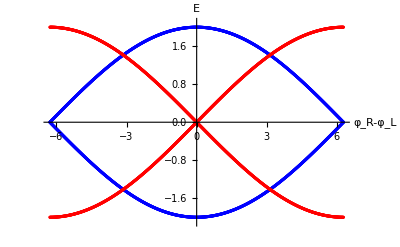

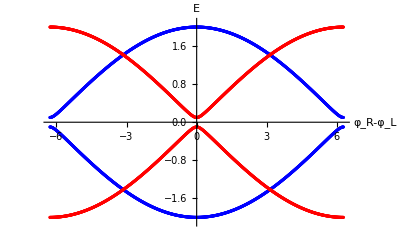

```mathematica
Do[
plte=ListPlot[Table[{ϕ,(eige/.{t->1,q0->1})[[i]]},{i,1,2},{ϕ,-2π,2π,π/256}],PlotStyle->Blue];
plto=ListPlot[Table[{ϕ,(eigo/.{t->1,q0->1})[[i]]},{i,1,2},{ϕ,-2π,2π,π/256}],PlotStyle->Red];
Print@Show[plte,plto,PlotRange->{{-2π,2π},{-2.1,2.1}},AxesLabel->{Subscript[φ, R]-Subscript[φ, L],"E"}],
{ϵ,{0.0,0.2}}
]
```

## 2次摂動：エネルギー振幅(係数)の計算

```mathematica
normN=((L+1)/2)^(-1/2);
normS=(2∑_(j=1)^100 Abs[((-μs+√(μs^2+Δs^2-1))/(1+Δs))^j-((-μs-√(μs^2+Δs^2-1))/(1+Δs))^j]^2)^(-1/2);
```

```mathematica
Amp2[μs_,Δs_,L_]:=((L+1)∑_(j=1)^100 Abs[((-μs+√(μs^2+Δs^2-1))/(1+Δs))^j-((-μs-√(μs^2+Δs^2-1))/(1+Δs))^j]^2)^-1 Abs[μs^2+Δs^2-1]/(1+Δs)^2∑_(q=1)^L (2(-1)^q Sin[(π q)/(L+1)]^2)/(μs+Cos[(π q)/(L+1)])
enzeros[L_]:=Table[{Cos[(π q)/(L+1)],0},{q,1,L}]
```

```mathematica
Do[
amp2data=Quiet[Table[{μs,0.001^2 Abs[Amp2[μs,0.8,L]]},{μs,-0.98,0.98,0.02}]];
amp2data=amp2data/.{Infinity->Inf,Indeterminate->Inf};
Export[FileNameJoin[{NotebookDirectory[],"../data/amp2mudep_t1.000_l0.001_d0.800_p0.000_L00"<>ToString[L]<>".csv"}],amp2data],
{L,3,6}
]
```

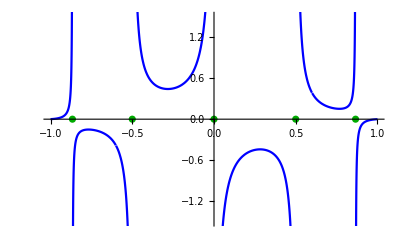

-Graphics-

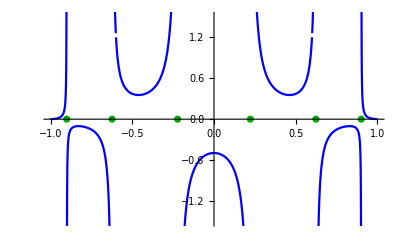

-Graphics-

```mathematica
Do[
plt1=ListPlot[Evaluate@enzeros[L],PlotStyle->Darker[Green]];
plt2=Plot[Evaluate@Amp2[μs,0.8,L],{μs,-1,1},PlotStyle->Blue];
contour1=ContourPlot[Evaluate@Amp2[μs,Δs,L],{μs,-1,1},{Δs,0,2},Contours->60,ContourStyle->None,
ColorFunction->(ColorData["LightTemperatureMap"][Rescale[#,{-1.5,1.5}]]&),ColorFunctionScaling->False,PlotLegends->Automatic];
contour2=ContourPlot[∏_(q=1)^L (μs+Cos[(π q)/(L+1)])==0,{μs,-1,1},{Δs,0,2},ContourStyle->Darker[Green]];
Print@Show[plt1,plt2,PlotRange->{-1.5,1.5},AxesLabel->{μs},ImageSize->400];
Print@Show[contour1,contour2,FrameLabel->{μs,Δs}],
{L,5,6}
]
```

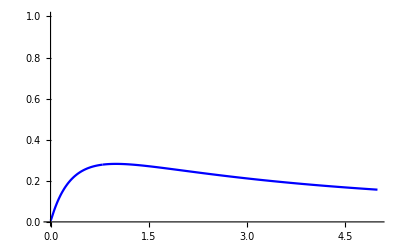

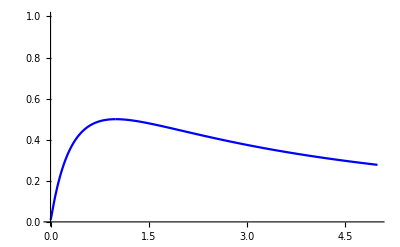

```mathematica
Do[
plt1=Plot[Evaluate@Amp2[-0.3(1-(-1)^L),Δs,L],{Δs,0,5},PlotStyle->Blue];
Print@Show[plt1,PlotRange->{0,1},AxesLabel->{Δs},ImageSize->400],
{L,7,8}
]
```

## 1次摂動：エネルギー振幅(係数)の計算

```mathematica
Amp1[q0_,Δs_,L_]:=(2((L+1)∑_(j=1)^100 Abs[((-μs+√(μs^2+Δs^2-1))/(1+Δs))^j-((-μs-√(μs^2+Δs^2-1))/(1+Δs))^j]^2)^(-1/2)(Abs[μs^2+Δs^2-1]^(1/2))/(1+Δs)Sin[(π q0)/(L+1)])/.{μs->-Cos[(π q0)/(L+1)]}
```

```mathematica
Do[
amp1data=Quiet[Table[{N[-Cos[(π q0)/(L+1)]],0.001Abs[Amp1[q0,0.8,L]]},{q0,1,L}]];
amp1data=amp1data/.{Infinity->Inf,Indeterminate->Inf};
Export[FileNameJoin[{NotebookDirectory[],"../data/amp1mudep_t1.000_l0.001_d0.800_p0.000_L00"<>ToString[L]<>".csv"}],amp1data],
{L,3,6}
]
```

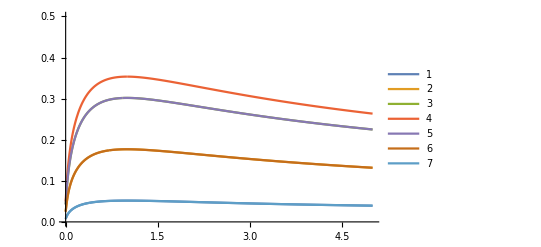

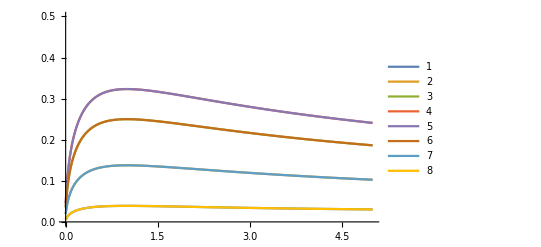

```mathematica
Do[
plt1=Plot[Evaluate@Table[Amp1[q0,Δs,L],{q0,1,L}],{Δs,0,5},PlotLegends->Automatic];
Print@Show[plt1,PlotRange->{0,0.5},AxesLabel->{Δs},ImageSize->400],
{L,7,8}
]
```

## その他

```mathematica
Simplify[Solve[(z^2(1/4(t^2-Δ^2)(z+z^-1)^2+μ t(z+z^-1)+(μ^2+Δ^2-ϵ^2))/.{ϵ->0})==0,z]]
```

{{z→-(μ+√(-t^2+Δ^2+μ^2))/(t-Δ)},{z→-(μ+√(-t^2+Δ^2+μ^2))/(t+Δ)},{z→(-μ+√(-t^2+Δ^2+μ^2))/(t-Δ)},{z→(-μ+√(-t^2+Δ^2+μ^2))/(t+Δ)}}

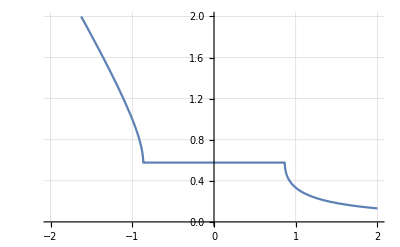

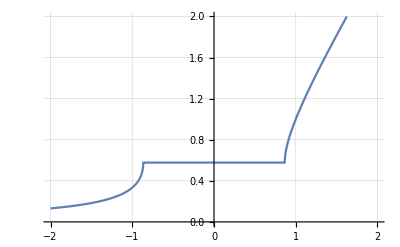

```mathematica
Plot[Abs[(-μs+√(μs^2-1^2+Δs^2))/(1+Δs)]/.{Δs->0.5},{μs,-2,2},PlotRange->{0,2},GridLines->Automatic,PlotLegends->Automatic]
Plot[Abs[(-μs-√(μs^2-1^2+Δs^2))/(1+Δs)]/.{Δs->0.5},{μs,-2,2},PlotRange->{0,2},GridLines->Automatic,PlotLegends->Automatic]
(*Plot[Abs[(-μs+√(μs^2-1^2+Δs^2))/(1-Δs)]/.{Δs->0.5},{μs,-2,2},PlotRange->{0,2},GridLines->Automatic,PlotLegends->Automatic]
Plot[Abs[(-μs-√(μs^2-1^2+Δs^2))/(1-Δs)]/.{Δs->0.5},{μs,-2,2},PlotRange->{0,2},GridLines->Automatic,PlotLegends->Automatic]*)
```

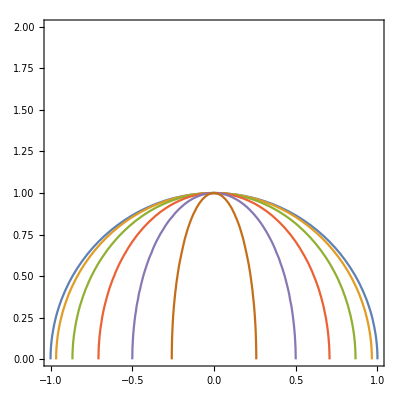

```mathematica
EzeroFunc[μ_,Δ_,n_]:=Module[{tab},
tab=Table[μ^2 Sec[(π p)/(n+1)]^2+Δ^2==1,{p,1,Floor[n/2]}];
Join[{μ^2+Δ^2==1},tab]
]
ContourPlot[Evaluate@EzeroFunc[μ,Δ,11],{μ,-1,1},{Δ,0,2}]
```

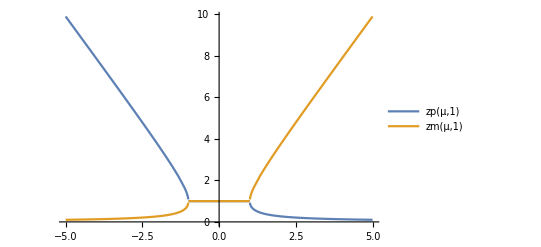

```mathematica
zp[μ_,t_]:=Abs[(-μ+√(μ^2-t^2))/t]
zm[μ_,t_]:=Abs[(-μ-√(μ^2-t^2))/t]
Plot[{zp[μ,1],zm[μ,1]},{μ,-5,5},PlotLegends->"Expressions"]
```

```mathematica
FullSimplify[∑_(j=1)^l (Sin[(π q j)/(l+1)])^2,{l∈Integers,q∈Integers}]
```

1/4 (1+2 l-Csc[(π q)/(1+l)] Sin[((1+2 l) π q)/(1+l)])